```mathematica
tmpquad=tmpIdx[[1]]
var=q[2];

CompleteSquare[quadratic_,var_]:=
(*Find square of quadradic polynomial, quadratic, with var as variable.  Assumes q[], k, and h as vectors.  Returns (h^2+D) and substitutions to create quadradic in h. *)
Module[{subsimple={Dot[a_,a_]->a^2,k^2->-m^2},tmpId,tmp,tmps,tmpr,tmpD,tmpc,tmpq2fac,sub,subD,dvar},
tmpId=quadratic/.(a_)^2->Dot[a,a];
(*manipulate k,q as vectors*)
dotRetain[{q[_],k},tmpId];
tmpId=tmpId//.simpleDot/.subsimple//Expand;
"Factor of power function. Find squre expression of var.";
tmpId=Collect[tmpId,{var}];
tmpId=groupDot[var,tmpId];
"The square of quadratic in var.";
tmpc=CoefficientList[tmpId,{var}];
tmpq2fac=tmpc//Last;
tmp=(tmpId//Last);(*first order in var*)
"Coefficient of linear term.";
tmp=(tmp/.var->1/2/.xDot->Times)//Expand;
"The transform of var that generates D^2->var^2 tmpq1fac";
tmpD=(var+tmp/tmpq2fac)√tmpq2fac//Simplify;
"Find remainder:";
tmps=dotRetain[{q[_],k},tmpD.tmpD]/.subsimple;
tmpr=tmpId-tmps/.xDot->Dot//Expand;
"Should not have any var.";
tmpr= dotRetain[{q[_],k},tmpr]//Simplify;
"Find linear transform h[var] to yield form (h^2+D) in denominator where h is new integration variable.";
sub=h==tmpD ;
sub=Solve[sub,var][[1,1]];" and ";
(*reinsert Dot for squared terms *)
tmps=tmps /.sub/.a_^2->a.a;Yield;
tmps=dotRetain[{q[_],k,h},tmps]/.subsimple//.simpleDot/.commuteDot//Simplify;
tmpr=dotRetain[{q[_],k,h},tmpr]/.subsimple//.simpleDot/.commuteDot//Simplify;
tmp=tmps+D;

subD=D->tmpr;
dvar=d[var]->d[h]D[sub[[2]],h];
{tmp,subD,dvar,sub}

]
CompleteSquare[tmpquad,q[1]]
```

(m^2+(q_1^1)^2) x_1^1+(m^2+(q_2^2)^2) x_2^2+(m^2+(k-q_1^1-q_2^2)^2) x_3^3

{D+h^2,D→1/(x_1^1+x_3^3)(m^2 (x_1^1)^2+x_3^3 ((m^2+(q_2^2)^2) x_2^2+m^2 x_3^3)+x_1^1 ((m^2+(q_2^2)^2) x_2^2+(m^2-2 k.q_2^2+(q_2^2)^2) x_3^3)),d[q_1^1]→d[h]/(√(x_1^1+x_3^3)),q_1^1→(k x_3^3-q_2^2 x_3^3+h √(x_1^1+x_3^3))/(x_1^1+x_3^3)}

```mathematica
"Check integration"
```

```mathematica
quadratic /.a_^2->a.a;
tmp0=dotRetain[{q[_],k},%]/.simpleDot/.commuteDot
tmp=D+h^2/.{tlist[[2]],tlist[[4]]}/.a_^2->a.a;
tmp=tmp//Simplify;
tmp=dotRetain[{q[_],k},tmp]/.simpleDot/.commuteDot//FullSimplify;
tmp=tmp/.simpleDot
tmp-tmp0//Simplify
//
tmp=tlist[[1,2]]/.tlist[[2]]//Denominator//Simplify;
Map[1/(#/d[h])&,tlist[[3]]][[2]]tmp
//
sub=Solve[Apply[Equal,tlist[[3]]],d[h]][[1,1,2]]/.d[_]->1
tmp[[2]]=tmp[[2]]sub;
tmp
sub=Solve[Apply[Equal,tlist[[4]]],h][[1,1]];
tmpb=tmp[[2]]/.sub//Simplify;
tmpa=evalDeltaIntOver[tmpI,q[3]][[2]];
tmpa-tmpb/.DiracDelta[_]->1//FullSimplify
```

m^2 x_1^1+q_1^1.q_1^1 x_1^1+m^2 x_2^2+q_2^2.q_2^2 x_2^2+m^2 x_3^3+k.k x_3^3-2 k.q_1^1 x_3^3-2 k.q_2^2 x_3^3+q_1^1.q_1^1 x_3^3+2 q_1^1.q_2^2 x_3^3+q_2^2.q_2^2 x_3^3

(m^2+q_1^1.q_1^1) x_1^1+(m^2+q_2^2.q_2^2) x_2^2+(m^2+k.k-2 k.q_1^1-2 k.q_2^2+q_1^1.q_1^1+2 q_1^1.q_2^2+q_2^2.q_2^2) x_3^3

0

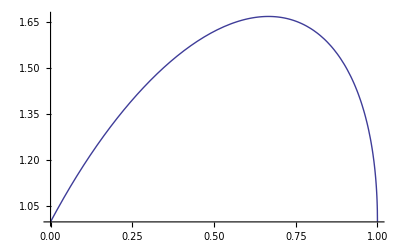

```mathematica
Plot[x+√(1+2x-3 (x)^2),{x,0,1}]
```

```mathematica
Series[Log[1+f],{f,0,2}]
Series[Exp[f],{f,0,2}]
```

f-f^2/2+O[f]^3

1+f+f^2/2+O[f]^3